# Ques_04: Integrals.

1. Calculate the indefinite integral of the function   f(x)=(x-√(arctan(2x)))/(1+4 x^2)  .

```mathematica
∫   (x-√ArcTan[2x])/(1+4 x^2)ⅆx
```

-1/3 ArcTan[2 x]^(3/2)+1/8 Log[1+4 x^2]

Now we can calculate the same integral using another method. (It is not an exercise, just only another way of solving the same exercise)

```mathematica
∫   (x-√ArcTan[2x])/(1+4 x^2)ⅆx=∫   x/(1+4 x^2)ⅆx -∫   (√ArcTan[2x])/(1+4 x^2)ⅆx
```

-1/3 ArcTan[2 x]^(3/2)+1/8 Log[1+4 x^2]

```mathematica
∫   x/(1+4 x^2)ⅆx ;t=1+4 x^2;
```

```mathematica
∫   x/(1+4 x^2)ⅆx=1/8∫   1/t ⅆt= 1/8 Log[t]=1/8 Log[1+4 x^2]
```

1/8 Log[1+4 x^2]

we can do the second  integral doing the change of variable t=ArcTan[2 x]

```mathematica
dt=D[ArcTan[2 x],x]
```

2/(1+4 x^2)

∫   (√ArcTan[2x])/(1+4 x^2)ⅆx=1/2∫   √t ⅆt =1/2 t^(3/2)/(3/2)=(ArcTan[2 x])^(3/2)/3

```mathematica
1/2∫   √t ⅆt
```

1/2 ∫√(1+4 x^2)ⅆ(1+4 x^2)

```mathematica
%/. t->ArcTan[2 x]
```

1/2 ∫√ArcTan[2 x]ⅆArcTan[2 x]

if you undo the change of variable 1/2 t^(3/2)/(3/2)=(ArcTan[2 x])^(3/2)/3

2 .	Graphically represent the region enclosed by the functions f(x)=x^2 and  g(x)=2 x+1. Calculate the area between the functions

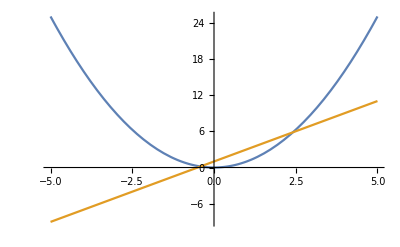

```mathematica
Plot[{x^2,2x+1},{x,-5,5}]
```

```mathematica
Solve[{x^2==2x+1},x]
```

{{x→1-√2},{x→1+√2}}

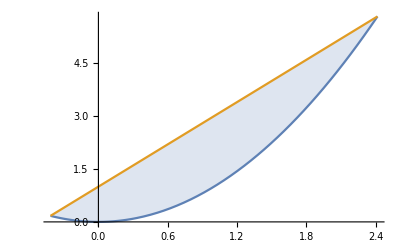

```mathematica
Plot[{x^2,2x+1},{x,1-√2,1+√2},Filling->{1->{2}}]
```

```mathematica
∫_(1-√2)^(1+√2) (2x+1-x^2) ⅆx
```

(8 √2)/3

Area=  (8 √2)/3

3. 	a) Obtain  the approximated value of the integral ∫_0^1 Cos[x]/(x+1)ⅆx using the trapezoidal rule with n=10.
            b) Calculate the second derivative of  f(x)= Cos[x]/(x+1)and using the adequate graph find M2, bound the error of the approximation of a) and calculate the number of exacts digits obtained
     c) Obtain the result of the integral using Mathematica 

```mathematica
NIntegrate[Cos[x]/(x+1),{x,0,1}]
```

0.601044

```mathematica
D[Cos[x]/(x+1),{x,2}]
```

(2 Cos[x])/(1+x)^3-Cos[x]/(1+x)+(2 Sin[x])/(1+x)^2

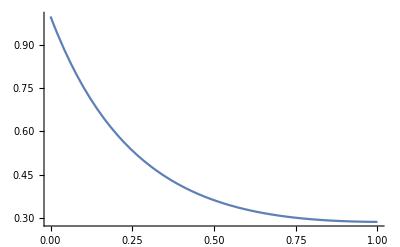

```mathematica
Plot[Abs[(2 Cos[x])/(1+x)^3-Cos[x]/(1+x)+(2 Sin[x])/(1+x)^2],{x,1,0}]
```

```mathematica
Trapezoid[a_,b_,n_,d_,f_]:=N[(f[a]+f[b]+2 ∑_(k=1)^(n-1) f[a+k ((b-a)/n)])((b-a)/(2  n)),d]
ErrorTrapezoid[a_,b_,n_,M2_]:= (b-a)^3/(12 n^2)M2;
```

```mathematica
ExactTrapezoid[a_,b_,n_,f_]:=(f[a]+f[b]+2 ∑_(k=1)^(n-1) f[a+k ((b-a)/n)])((b-a)/(2  n));
```

```mathematica
Trapezoid[0,1,10,20,f]
```

0.60141412919716912939

```mathematica
N[%,20]
```

0.60141412919716912939

```mathematica
ExactTrapezoid[a_,b_,n_,f_]:=(f[a]+f[b]+2 ∑_(k=1)^(n-1) f[a+k ((b-a)/n)])((b-a)/(2  n))
```

```mathematica
ExactTrapezoid[0,1,10,f]
```

1/20 (1+2 (10/11 Cos[1/10]+5/6 Cos[1/5]+10/13 Cos[3/10]+5/7 Cos[2/5]+2/3 Cos[1/2]+5/8 Cos[3/5]+10/17 Cos[7/10]+5/9 Cos[4/5]+10/19 Cos[9/10])+Cos[1]/2)

```mathematica
N[1/20 (1+2 (10/11 Cos[1/10]+5/6 Cos[1/5]+10/13 Cos[3/10]+5/7 Cos[2/5]+2/3 Cos[1/2]+5/8 Cos[3/5]+10/17 Cos[7/10]+5/9 Cos[4/5]+10/19 Cos[9/10])+Cos[1]/2)]
```

0.601414

```mathematica
ErrorTrapezoid[0,1,10,1]
```

1/1200

```mathematica
N[%]
```

0.000833333

The approximated value of        ∫_0^1 Cos[x]/(x+1)ⅆx usign the trapezoidal rule with 10 subdivisions is     ∫_0^1 Cos[x]/(x+1)≈    0.601414129     
             and the value of M2=        1               and the number of exact digits obtained is 2

The approximation obtained with Mathematica is (use NIntegrate)∫_0^1 Cos[x]/(x+1)≈0.601044